6.07098

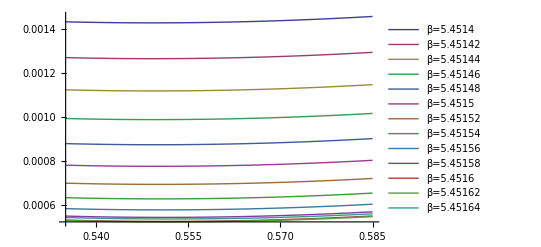

{5.45161,0.551409,0.000521719,{-0.184709,0.184709}}

{5.45389,0.58827,0.00101355,{-0.0831794,0.0831794}}

Parameters of the scan: β∈["5.33478","5.33479"] with δβ="1." × 10^"-6"   ν∈["0.36","0.42"] with δν="0.001"   Δx="0.5"*Δx_max

Time to perform calculation: 4843.856000

{{{5.33479,4.83756×10^-6},{0.389,0.0194901},{-0.551094,0.551094}}}

Parameters of the scan: β∈["5.33478","5.33479"] with δβ="1." × 10^"-6"   ν∈["0.36","0.42"] with δν="0.001"   Δx="0.4"*Δx_max

Time to perform calculation: 4259.108000

{{{5.33479,4.82798×10^-6},{0.389,0.0197313},{-0.442288,0.442288}}}

Parameters of the scan: β∈["5.33478","5.33479"] with δβ="1." × 10^"-6"   ν∈["0.36","0.42"] with δν="0.001"   Δx="0.3"*Δx_max

Time to perform calculation: 3222.668000

{{{5.33479,4.82915×10^-6},{0.389,0.0198969},{-0.332776,0.332776}}}

Parameters of the scan: β∈["5.33478","5.33479"] with δβ="1." × 10^"-6"   ν∈["0.36","0.42"] with δν="0.001"   Δx="0.2"*Δx_max

Time to perform calculation: 2180.608000

{{{5.33479,4.82484×10^-6},{0.388,0.0199452},{-0.226571,0.226571}}}

Parameters of the scan: β∈["5.33478","5.33479"] with δβ="1." × 10^"-6"   ν∈["0.36","0.42"] with δν="0.001"   Δx="0.1"*Δx_max

Time to perform calculation: 2180.544000

{{{5.33479,4.82345×10^-6},{0.388,0.0199884},{-0.113646,0.113646}}}

(  5.334788000000e+00 |   4.837561368948e-06 |   3.890000000000e-01 |   1.949012580770e-02 |  -5.510937387137e-01 |   5.510937387137e-01
  5.334787000000e+00 |   4.827983429794e-06 |   3.890000000000e-01 |   1.973125632087e-02 |  -4.422880518397e-01 |   4.422880518397e-01
  5.334786000000e+00 |   4.829151478091e-06 |   3.890000000000e-01 |   1.989688055952e-02 |  -3.327758345313e-01 |   3.327758345313e-01
  5.334786000000e+00 |   4.824840308065e-06 |   3.880000000000e-01 |   1.994523060784e-02 |  -2.265714124499e-01 |   2.265714124499e-01
  5.334785000000e+00 |   4.823447314766e-06 |   3.880000000000e-01 |   1.998837452121e-02 |  -1.136464887289e-01 |   1.136464887289e-01)

Minimizing numerically for: β∈["5.334","5.335"]   and for  ν∈["0.3","0.46"]   with   Δx="0.5"*Δx_max

Time to perform calculation: 74937.956000

{{{5.33479,0.0000385754},{0.388972,0.0125609},{-0.551933,0.551933}}}

Minimizing numerically for: β∈["5.334","5.335"]   and for  ν∈["0.3","0.46"]   with   Δx="0.4"*Δx_max

Time to perform calculation: 60956.868000

{{{5.33479,0.0000384247},{0.389011,0.012401},{-0.442322,0.442322}}}

Minimizing numerically for: β∈["5.334","5.335"]   and for  ν∈["0.3","0.46"]   with   Δx="0.3"*Δx_max

Time to perform calculation: 49692.100000

{{{5.33479,0.0000383171},{0.388908,0.0122385},{-0.33317,0.33317}}}

Minimizing numerically for: β∈["5.334","5.335"]   and for  ν∈["0.3","0.46"]   with   Δx="0.2"*Δx_max

Time to perform calculation: 35832.556000

{{{5.33479,0.000038256},{0.388262,0.0119975},{-0.22552,0.22552}}}

Minimizing numerically for: β∈["5.334","5.335"]   and for  ν∈["0.3","0.46"]   with   Δx="0.1"*Δx_max

Time to perform calculation: 27367.952000

{{{5.33479,0.0000382212},{0.388049,0.0119333},{-0.113378,0.113378}}}

(  5.334787707664e+00 |   3.857542803543e-05 |   3.889720991916e-01 |   1.256086087887e-02 |  -5.519334464111e-01 |   5.519334464111e-01
  5.334786900483e+00 |   3.842471525174e-05 |   3.890114663684e-01 |   1.240100405964e-02 |  -4.423221466081e-01 |   4.423221466081e-01
  5.334786234851e+00 |   3.831714449351e-05 |   3.889080176433e-01 |   1.223851268028e-02 |  -3.331700951951e-01 |   3.331700951951e-01
  5.334785727492e+00 |   3.825596686112e-05 |   3.882616145357e-01 |   1.199746040934e-02 |  -2.255199406953e-01 |   2.255199406953e-01
  5.334785419918e+00 |   3.822120268630e-05 |   3.880488449118e-01 |   1.193328490762e-02 |  -1.133780357695e-01 |   1.133780357695e-01)

```mathematica
Needs["ErrorBarPlots`"]
SetOptions[$FrontEndSession,PrintPrecision->10]
AppendTo[$Path,"/home/sciarra/Script/CollapsePlot/BashMathematica"];
If[FindFile["AnalyticCollapse`"]===$Failed,Print["Package \"AnalyticCollapse\" could not be loaded! Aborting..."];Abort[],Get["AnalyticCollapse`"]]
(*----------------------------------------------------------------------------------*)
(*The datafile must be in the format: {{Beta, Kurtosis}}*)
NamesOfFiles={
"/home/work-itp/sciarra/StaggeredProject/Nf2/muiPiT/mass0100/nt6/AnalyticCollapse/muiPiT_mass0100_nt6_ns12_poly_im_withZeroMean_reweighted.dat",
"/home/work-itp/sciarra/StaggeredProject/Nf2/muiPiT/mass0100/nt6/AnalyticCollapse/muiPiT_mass0100_nt6_ns18_poly_im_withZeroMean_reweighted.dat",
"/home/work-itp/sciarra/StaggeredProject/Nf2/muiPiT/mass0100/nt6/AnalyticCollapse/muiPiT_mass0100_nt6_ns24_poly_im_withZeroMean_reweighted.dat"
};
(*The estimator datafile must be in the format: {{EstimatorNumber, Beta, Kurtosis}}*)
NamesOfFilesWithEstimators=StringInsert[#,"_estimators",-5]&/@NamesOfFiles;
(*----------------------------------------------------------------------------------*)
(*Checks on the existence of the files*)
If[!FileExistsQ[#],Print[StringForm["File \"``\" not found! Aborting...",#]];Abort[]]&/@Join[NamesOfFiles,NamesOfFilesWithEstimators];

(*Check on the name of the files:they must contain "ns" with at least one digit afterwards*)
If[Length[StringCases[#,RegularExpression["ns[[:digit:]]+"]]]≠1,
Print[StringForm["File \"``\" does not contain one and only one occurence of \"ns[[::digit]]+\"! Aborting...",#]];Abort[]
]&/@StringReplace[NamesOfFiles,RegularExpression[".*/"]->""];
(*----------------------------------------------------------------------------------*)
(*Import data*)
Volume[filename_]:=
Module[{basename},
basename=StringReplace[filename,RegularExpression[".*/"]->""];
ToExpression[StringCases[StringCases[basename,RegularExpression["ns[[:digit:]]+"]],RegularExpression["[[:digit:]]+"]][[1,1]]]
]
AllDataInBeta={Import[#],Volume[#]}&/@NamesOfFiles;
AllEstimatorsInBeta={Import[#],Volume[#]}&/@NamesOfFilesWithEstimators;
(*----------------------------------------------------------------------------------*)

If[False,
MinimizeNumericallyQualityOfCollapse[AllDataInBeta,5.451,5.452,0.25,0.75,0.5],
scanResult=AbsoluteTiming[MakeScanInBetaCAndNu[AllDataInBeta,5.4514,5.45164,0.00002,0.535,0.585,0.001,0.1]];
Print[scanResult[[1]]]; MakePlotOfScanSeparatingBlocksOfBetas[scanResult[[2]]]
]
```